```mathematica
u[x_, y_] := Log[x] + Log[y]
min = -5
max = u[100, 100]
```

-5

2 Log[100]

-7

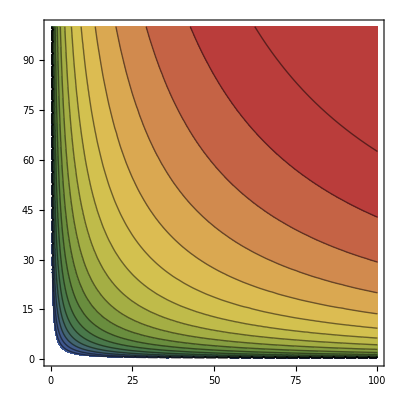

```mathematica
utilcontour = 
ContourPlot[u[x, y], {x, 0, 100}, {y, 0, 100},
Contours->20,
ColorFunction->"DarkRainbow"]
```

```mathematica
utilsurface =
Plot3D[u[x, y], {x, 0, 100}, {y, 0, 100},
PlotRange->{0, max},
Mesh->20, MeshFunctions->{#3&}, ClippingStyle->None,
ColorFunction->"DarkRainbow", PlotStyle->Opacity[0.5]]
```

-Graphics3D-

```mathematica
Show[utilsurface,Graphics3D[utilcontour[[1]]/. {x_Real,y_Real}:>{x,y,min}],BoxRatios->{1,1,0.6},FaceGrids->{Back,Left}, PlotRange->Automatic,
AxesLabel->{"Good X", "Good Y",Utility},
TicksStyle->Directive[FontOpacity->0,FontSize->0]]
```

-Graphics3D-

```mathematica
Show[utilsurface,Graphics3D[utilcontour[[1]]/. {x_Real,y_Real}:>{x,y,min}],BoxRatios->{1,1,0.6},FaceGrids->{Back,Left}, PlotRange->Automatic]
```

-Graphics3D-

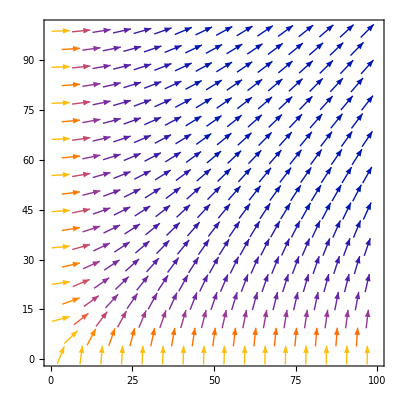

```mathematica
utilvector = VectorPlot[{1/x, 1/y}, {x, 0, 100}, {y, 0, 100}]
```